```mathematica
<<Quaternions`
```

```mathematica
q=Quaternion[1,2,3,4]
```

Quaternion[1,2,3,4]

```mathematica
Conjugate[q]
```

Quaternion[1,-2,-3,-4]

```mathematica
q**Conjugate[q]
```

Quaternion[30,0,0,0]

```mathematica
1+2^2+3^2+4^2
```

30

```mathematica
q^2**(q-1)-(q-1)**q^2
```

Quaternion[0,0,0,0]

```mathematica
q^2
```

Quaternion[-28,4,6,8]

```mathematica
f[d_,n_]:=2^(d+n-2)Gamma[d/2]Gamma[1/2(d+n-1)]/(Sqrt[π]Gamma[d+n/2-1])
```

```mathematica
Table[f[d,2n],{d,1,8},{n,1,8}]//Grid
```

2 | 8 | 32 | 128 | 512 | 2048 | 8192 | 32768
2 | 6 | 20 | 70 | 252 | 924 | 3432 | 12870
2 | 16/3 | 16 | 256/5 | 512/3 | 4096/7 | 2048 | 65536/9
2 | 5 | 14 | 42 | 132 | 429 | 1430 | 4862
2 | 24/5 | 64/5 | 256/7 | 768/7 | 1024/3 | 16384/15 | 196608/55
2 | 14/3 | 12 | 33 | 286/3 | 286 | 884 | 8398/3
2 | 32/7 | 80/7 | 640/21 | 256/3 | 8192/33 | 8192/11 | 327680/143
2 | 9/2 | 11 | 143/5 | 78 | 221 | 646 | 1938

```mathematica
Mean[Table[
{a,b,c,d}=Normalize[RandomVariate[NormalDistribution[0,1],4]];
a^2,{i,1,1000000}]]
```

0.249986

```mathematica
Mean[Table[
{a,b,c,d}=Normalize[RandomVariate[NormalDistribution[0,1],4]];
a^4,{i,1,1000000}]]
```

0.125249

```mathematica
Mean[Table[
{a,b,c,d}=Normalize[RandomVariate[NormalDistribution[0,1],4]];
(a^2+b^2+c^2+d^2),{i,1,1000000}]]
```

1.

```mathematica
Clear[a,b,c,d]
```

```mathematica
Expand[(a^2+b^2+c^2+d^2)^2]
```

a^4+2 a^2 b^2+b^4+2 a^2 c^2+2 b^2 c^2+c^4+2 a^2 d^2+2 b^2 d^2+2 c^2 d^2+d^4

```mathematica
Mean[Table[
{a,b,c,d}=Normalize[RandomVariate[NormalDistribution[0,1],4]];
a^4+2 a^2 b^2+b^4+2 a^2 c^2+2 b^2 c^2+c^4+2 a^2 d^2+2 b^2 d^2+2 c^2 d^2+d^4,{i,1,1000000}]]
```

1.

```mathematica
Mean[Table[
{a,b,c,d}=Normalize[RandomVariate[NormalDistribution[0,1],4]];
4 a^4+2 a^2 b^2+2 a^2 c^2+2 b^2 c^2+2 a^2 d^2+2 b^2 d^2+2 c^2 d^2,{i,1,1000000}]]
```

1.00127

```mathematica
Mean[Table[
{a,b,c,d}=Normalize[RandomVariate[NormalDistribution[0,1],4]];
4 a^4+12 a^2 b^2,{i,1,1000000}]]
```

1.00077

```mathematica
Mean[Table[
{a,b,c,d}=Normalize[RandomVariate[NormalDistribution[0,1],4]];
4 a^4+12 a^2 b^2,{i,1,1000000}]]
```

0.999163

```mathematica
Mean[Table[
{a,b,c,d}=Normalize[RandomVariate[NormalDistribution[0,1],4]];
a^2 b^2,{i,1,1000000}]]
```

0.0416285

```mathematica
(1-4/8)/12//N
```

0.0416667

```mathematica
(a+b+c+d)^4//Expand
```

a^4+4 a^3 b+6 a^2 b^2+4 a b^3+b^4+4 a^3 c+12 a^2 b c+12 a b^2 c+4 b^3 c+6 a^2 c^2+12 a b c^2+6 b^2 c^2+4 a c^3+4 b c^3+c^4+4 a^3 d+12 a^2 b d+12 a b^2 d+4 b^3 d+12 a^2 c d+24 a b c d+12 b^2 c d+12 a c^2 d+12 b c^2 d+4 c^3 d+6 a^2 d^2+12 a b d^2+6 b^2 d^2+12 a c d^2+12 b c d^2+6 c^2 d^2+4 a d^3+4 b d^3+4 c d^3+d^4

```mathematica
4+12 4+6 6+12 12+24
```

256

```mathematica
Mean[Table[
{a,b,c,d}=Normalize[RandomVariate[NormalDistribution[0,1],4]];
a^3 b,{i,1,1000000}]]
```

-0.0000593243

```mathematica
Mean[Table[
{a,b,c,d}=Normalize[RandomVariate[NormalDistribution[0,1],4]];
4 a^4+12 a^2 b^2,{i,1,1000000}]]
```

0.998844

```mathematica
Mean[Table[
{a,b,c,d}=Normalize[RandomVariate[NormalDistribution[0,1],4]];
a^4+4 a^3 b+6 a^2 b^2+4 a b^3+b^4+4 a^3 c+12 a^2 b c+12 a b^2 c+4 b^3 c+6 a^2 c^2+12 a b c^2+6 b^2 c^2+4 a c^3+4 b c^3+c^4+4 a^3 d+12 a^2 b d+12 a b^2 d+4 b^3 d+12 a^2 c d+24 a b c d+12 b^2 c d+12 a c^2 d+12 b c^2 d+4 c^3 d+6 a^2 d^2+12 a b d^2+6 b^2 d^2+12 a c d^2+12 b c d^2+6 c^2 d^2+4 a d^3+4 b d^3+4 c d^3+d^4,{i,1,1000000}]]
```

2.00044

```mathematica
Mean[Table[
{a,b,c,d}=Normalize[RandomVariate[NormalDistribution[0,1],4]];
(a+b+c+d)^4,{i,1,1000000}]]
```

1.99966

```mathematica
Mean[Table[
{a,b,c,d}=Normalize[RandomVariate[NormalDistribution[0,1],4]];
((a+b+c+d)/2)^2,{i,1,1000000}]]
```

0.250001

```mathematica
Mean[Table[
{a,b,c,d}=Normalize[RandomVariate[NormalDistribution[0,1],4]];
((a-1)^2+b^2+c^2+d^2)^4,{i,1,1000000}]]
```

41.9191

```mathematica
Table[CatalanNumber[n],{n,1,10}]
```

{1,2,5,14,42,132,429,1430,4862,16796}

```mathematica
Clear[a,b,c,d]
```

```mathematica
u=((a-1)^2+b^2+c^2+d^2)^4-(a^2+b^2+c^2+d^2)^4
```

((-1+a)^2+b^2+c^2+d^2)^4-(a^2+b^2+c^2+d^2)^4

1-8 a+28 a^2-56 a^3+70 a^4-56 a^5+28 a^6-8 a^7+4 b^2-24 a b^2+60 a^2 b^2-80 a^3 b^2+60 a^4 b^2-24 a^5 b^2+6 b^4-24 a b^4+36 a^2 b^4-24 a^3 b^4+4 b^6-8 a b^6+4 c^2-24 a c^2+60 a^2 c^2-80 a^3 c^2+60 a^4 c^2-24 a^5 c^2+12 b^2 c^2-48 a b^2 c^2+72 a^2 b^2 c^2-48 a^3 b^2 c^2+12 b^4 c^2-24 a b^4 c^2+6 c^4-24 a c^4+36 a^2 c^4-24 a^3 c^4+12 b^2 c^4-24 a b^2 c^4+4 c^6-8 a c^6+4 d^2-24 a d^2+60 a^2 d^2-80 a^3 d^2+60 a^4 d^2-24 a^5 d^2+12 b^2 d^2-48 a b^2 d^2+72 a^2 b^2 d^2-48 a^3 b^2 d^2+12 b^4 d^2-24 a b^4 d^2+12 c^2 d^2-48 a c^2 d^2+72 a^2 c^2 d^2-48 a^3 c^2 d^2+24 b^2 c^2 d^2-48 a b^2 c^2 d^2+12 c^4 d^2-24 a c^4 d^2+6 d^4-24 a d^4+36 a^2 d^4-24 a^3 d^4+12 b^2 d^4-24 a b^2 d^4+12 c^2 d^4-24 a c^2 d^4+4 d^6-8 a d^6

```mathematica
Mean[Table[
{a,b,c,d}=Normalize[RandomVariate[NormalDistribution[0,1],4]];
((a+b)/Sqrt[2])^2,{i,1,1000000}]]
```

0.249983

```mathematica
Mean[Table[
{a,b,c,d}=Normalize[RandomVariate[NormalDistribution[0,1],4]];
((a+b)/Sqrt[2])^4,{i,1,1000000}]]
```

0.124961

```mathematica
((x+y)/Sqrt[2])^4//Expand
```

x^4/4+x^3 y+(3 x^2 y^2)/2+x y^3+y^4/4

```mathematica
Clear[u,v,a,b,c,d]
```

```mathematica
Solve[{u+v==1,u/2+3v/2==1/2},{u,v}]
```

{{u→1,v→0}}

```mathematica
Mean[Table[
{a,b}=Normalize[RandomVariate[NormalDistribution[0,1],2]];
((a+b)/Sqrt[2])^2,{i,1,1000000}]]
```

0.500049

```mathematica
Mean[Table[
{a,b}=Normalize[RandomVariate[NormalDistribution[0,1],2]];
((a+b)/Sqrt[2])^4,{i,1,1000000}]]
```

0.374938

```mathematica
8*.375
```

3.

```mathematica
Mean[Table[
{a,b}=Normalize[RandomVariate[NormalDistribution[0,1],2]];
a^4,{i,1,1000000}]]
```

0.374781

```mathematica
((a+b)/Sqrt[2])^4//Expand
```

a^4/4+a^3 b+(3 a^2 b^2)/2+a b^3+b^4/4

```mathematica
Mean[Table[
{a,b}=Normalize[RandomVariate[NormalDistribution[0,1],2]];
a^4/2+(3 a^2 b^2)/2,{i,1,1000000}]]
```

0.374869

```mathematica
Mean[Table[
{a,b}=Normalize[RandomVariate[NormalDistribution[0,1],2]];
a^2 b^2,{i,1,1000000}]]
```

0.124974

```mathematica
Table[Mean[Table[
{a,b}=Normalize[RandomVariate[NormalDistribution[0,1],2]];
(2(1-a))^n,{i,1,100000}]],{n,1,10}]
```

{2.00079,6.00624,19.8771,69.9778,253.882,923.017,3407.25,12934.,48817.7,185057.}

```mathematica
1/(1-θ(1-x))//Expand
```

1/(1-(1-x) θ)

```mathematica
Table[Mean[Table[
{a,b}=Normalize[RandomVariate[NormalDistribution[0,1],2]];
2^n(1-a)^n,{i,1,100000}]],{n,1,10}]
```

{1.99622,5.97292,19.8629,70.0697,250.828,920.575,3448.36,12834.1,48809.9,185230.}

```mathematica
Sum[2^n(1-x)^n,{n,0,∞}]
```

1/(-1+2 x)

```mathematica
Sum[2^n(1-x)^n,{n,0,∞}]
```

```mathematica
Mean[Table[
{a,b}=Normalize[RandomVariate[NormalDistribution[0,1],2]];
(1-a)^2,{i,1,100000}]]
```

1.49591

```mathematica
u=Quaternion[1,2,3,4]
```

Quaternion[1,2,3,4]

```mathematica
v=Conjugate[u]
```

Quaternion[1,-2,-3,-4]

```mathematica
u**v-v**u
```

Quaternion[0,0,0,0]

```mathematica
Mean[Table[
{a,b}=Normalize[RandomVariate[NormalDistribution[0,1],2]];
(1-a)^2 b^2,{i,1,100000}]]
```

0.626415

```mathematica
Sum[CatalanNumber[n] x^n,{n,0,∞}]
```

(1-√(1-4 x))/(2 x)

```mathematica
Sum[CatalanNumber[n]x^n/n!,{n,0,∞}]
```

ⅇ^(2 x) (BesselI[0,2 x]-BesselI[1,2 x])

```mathematica
Integrate[Exp[-x^2/2]Exp[-y^2/2]Exp[-z^2/2]Exp[-w^2/2]/(2π)^2,{x,-∞,∞},{y,-∞,∞},{z,-∞,∞},{w,-∞,∞}]
```

1

```mathematica
Integrate[Exp[ⅈ λ (x^2+y^2+z^2+w^2-1)]Exp[θ x]Exp[-x^2/2]Exp[-y^2/2]Exp[-z^2/2]Exp[-w^2/2]/(2π)^2,{x,-∞,∞},{y,-∞,∞},{z,-∞,∞},{w,-∞,∞},Assumptions->{λ∈Reals}]
```

-(ⅇ^(-ⅈ (λ-θ^2/(2 ⅈ+4 λ))))/(ⅈ+2 λ)^2

```mathematica
Integrate[-(ⅇ^(-ⅈ (λ-θ^2/(2 ⅈ+4 λ))))/(ⅈ+2 λ)^2,{λ,-∞,∞}]
```

∫_(-∞)^∞ -(ⅇ^(-ⅈ (λ-θ^2/(2 ⅈ+4 λ))))/(ⅈ+2 λ)^2ⅆλ

```mathematica
Mean[Table[
{a,b}=Normalize[RandomVariate[NormalDistribution[0,1],2]];
(2(a-1))^2,{i,1,100000}]]
```

5.99379

```mathematica
((x+y)/Sqrt[2]-1)^4//Expand
```

1-2 √2 x+3 x^2-√2 x^3+x^4/4-2 √2 y+6 x y-3 √2 x^2 y+x^3 y+3 y^2-3 √2 x y^2+(3 x^2 y^2)/2-√2 y^3+x y^3+y^4/4

```mathematica
Mean[Table[
{a,b}=Normalize[RandomVariate[NormalDistribution[0,1],2]];
(a^2-1/2)(b^2-1/2),{i,1,100000}]]
```

-0.124687

```mathematica
Mean[Table[
{a,b}=Normalize[RandomVariate[NormalDistribution[0,1],2]];
(a^2-1/2),{i,1,100000}]]
```

0.00176426

```mathematica
Mean[Table[
{x,y}=Normalize[RandomVariate[NormalDistribution[0,1],2]];
r=RandomVariate[NormalDistribution[0,Sqrt[2]]];
r^4,{i,1,100000}]]
```

11.9758

```mathematica
Mean[Table[
{x,y}=Normalize[RandomVariate[NormalDistribution[0,1],2]];
r=RandomVariate[NormalDistribution[0,Sqrt[2]]];
(r x)^4,{i,1,1000000}]]
```

4.52991

```mathematica
Mean[Table[
{x,y}=Normalize[RandomVariate[NormalDistribution[0,1],2]];
r=RandomVariate[NormalDistribution[0,Sqrt[2]]];
x^4,{i,1,1000000}]]
```

0.374962

```mathematica
3/8*12
```

9/2

```mathematica
Mean[Table[
{x,y}=Normalize[RandomVariate[NormalDistribution[0,1],2]];
r=RandomVariate[NormalDistribution[0,Sqrt[2]]];
r^2,{i,1,1000000}]]
```

1.99796

```mathematica
Mean[Table[
{x,y}=Normalize[RandomVariate[NormalDistribution[0,1],2]];
r=RandomVariate[NormalDistribution[0,Sqrt[2]]];
(r x)^6,{i,1,1000000}]]
```

37.6098

```mathematica
Mean[Table[
{x,y}=Normalize[RandomVariate[NormalDistribution[0,1],2]];
(2(1-x))^6,{i,1,1000000}]]
```

926.724

```mathematica
Mean[Table[
{x,y}=Normalize[RandomVariate[NormalDistribution[0,1],2]];
x^2,{i,1,1000000}]]
```

0.500372

```mathematica
Mean[Table[
{x,y}=Normalize[RandomVariate[NormalDistribution[0,1],2]];
r=RandomVariate[NormalDistribution[0,Sqrt[2]]];
r^4,{i,1,1000000}]]
```

12.0011

```mathematica
(3+12)*16
```

240

```mathematica
Mean[Table[
{x,y}=Normalize[RandomVariate[NormalDistribution[0,1],2]];
x^4,{i,1,1000000}]]
```

0.376031

```mathematica
16*(3+3/8)
```

54

```mathematica
Mean[Table[
{x,y}=Normalize[RandomVariate[NormalDistribution[0,1],2]];
(2(1-x))^4,{i,1,1000000}]]
```

69.868

```mathematica
Mean[Table[
{x,y}=Normalize[RandomVariate[NormalDistribution[0,1],2]];
16(1-x)^4,{i,1,1000000}]]
```

69.9644

```mathematica
Mean[Table[
{x,y}=Normalize[RandomVariate[NormalDistribution[0,1],2]];
16(1+6 x^2+x^4),{i,1,1000000}]]
```

70.0158

```mathematica
Mean[Table[
{x,y}=Normalize[RandomVariate[NormalDistribution[0,1],2]];
16(4+x^4),{i,1,1000000}]]
```

69.998

```mathematica
16(4+3/8)
```

70

```mathematica
Clear[x,y]
```

```mathematica
Expand[((x+y)/Sqrt[2])^4]
```

x^4/4+x^3 y+(3 x^2 y^2)/2+x y^3+y^4/4

```mathematica
Expand[(1-x)^6]
```

1-6 x+15 x^2-20 x^3+15 x^4-6 x^5+x^6

```mathematica
32*(1+10/2+5 3/8)
```

252

```mathematica
Expand[((x+y)/Sqrt[2])^6]
```

x^6/8+(3 x^5 y)/4+(15 x^4 y^2)/8+(5 x^3 y^3)/2+(15 x^2 y^4)/8+(3 x y^5)/4+y^6/8

```mathematica
Mean[Table[
{x,y}=Normalize[RandomVariate[NormalDistribution[0,1],2]];
x^6,{i,1,1000000}]]
```

0.312504

```mathematica
Mean[Table[
{x,y}=Normalize[RandomVariate[NormalDistribution[0,1],2]];
x^4 y^2,{i,1,1000000}]]
```

0.0625545

```mathematica
.3125/0.0625
```

5.

```mathematica
Clear[x,y]
```

```mathematica
(x^2+y^2)^3//Expand
```

x^6+3 x^4 y^2+3 x^2 y^4+y^6

```mathematica
1/(2+6/5)
```

5/16

```mathematica
N[%]
```

0.3125

```mathematica
64(1+15/2+15 3/8+5/16)
```

924

```mathematica
Mean[Table[
{x,y}=Normalize[RandomVariate[NormalDistribution[0,1],2]];
z=x+ⅈ y,{i,1,100000}]]
```

-0.000667678-0.000713641 ⅈ

```mathematica
Mean[Table[
{x,y}=Normalize[RandomVariate[NormalDistribution[0,1],2]];
z=x+ⅈ y;
z*Conjugate[z],{i,1,100000}]]
```

1.+0. ⅈ

```mathematica
(1-c)^3(1-d)^3//Expand
```

1-3 c+3 c^2-c^3-3 d+9 c d-9 c^2 d+3 c^3 d+3 d^2-9 c d^2+9 c^2 d^2-3 c^3 d^2-d^3+3 c d^3-3 c^2 d^3+c^3 d^3

```mathematica
Mean[Table[
{x,y}=Normalize[RandomVariate[NormalDistribution[0,1],2]];
z=x+ⅈ y,{i,1,100000}]]
```

-0.0023887-0.00262116 ⅈ

```mathematica
Mean[Table[
{x,y}=Normalize[RandomVariate[NormalDistribution[0,1],2]];
z=x+ⅈ y;
z^2,{i,1,100000}]]
```

0.0035816-0.00314522 ⅈ

```mathematica
Mean[Table[
{x,y}=Normalize[RandomVariate[NormalDistribution[0,1],2]];
z=x+ⅈ y;
z^2 Conjugate[z],{i,1,100000}]]
```

-0.000427987-0.000837452 ⅈ

```mathematica
Mean[Table[
{x,y}=Normalize[RandomVariate[NormalDistribution[0,1],2]];
z=x+ⅈ y;
z^3 Conjugate[z],{i,1,100000}]]
```

0.00256288+0.000477469 ⅈ

```mathematica
Mean[Table[
{x,y}=Normalize[RandomVariate[NormalDistribution[0,1],2]];
z=x+ⅈ y;
z^3 Conjugate[z^3],{i,1,100000}]]
```

1.+0. ⅈ

```mathematica
Mean[Table[
{x,y}=Normalize[RandomVariate[NormalDistribution[0,1],2]];
z=x+ⅈ y;
z^2 Conjugate[z^2],{i,1,100000}]]
```

1.+0. ⅈ

```mathematica
Clear[b]
```

```mathematica
b[n_,r_]:=Binomial[n,r]
```

```mathematica
b[6,0]^2+b[6,2]^2+b[6,4]^2+b[6,6]^2
```

452

```mathematica
Sum[b[6,i]^2,{i,0,6}]
```

924

```mathematica
Clear[q,z,b,x,y,z,w]
```

```mathematica
<<Quaternions`
```

```mathematica
Mean[Table[
{x,y,z,w}=Normalize[RandomVariate[NormalDistribution[0,1],4]];
q=Quaternion[x,y,z,w];
r=Conjugate[q];
(1-2q+q**q)**(1-2r+r**r),{i,1,1000}]]
```

Quaternion[4.81429,0.,0.,0.]

```mathematica
q**r-r**q
```

Quaternion[0.,0.,0.,0.]

```mathematica
q**r**r-r**r**q
```

Quaternion[-4.16334×10^-17,0.,0.,2.77556×10^-17]

```mathematica
Mean[Table[
{x,y,z,w}=Normalize[RandomVariate[NormalDistribution[0,1],4]];
q=Quaternion[x,y,z,w];
r=Conjugate[q];
1-2 q+q^2-2 r+4 q**r-2 q^2**r+r^2-2 q**r^2+q^2**r^2,{i,1,1000}]]
```

Quaternion[4.94904,1.33353×10^-16,1.16212×10^-16,3.25124×10^-17]

```mathematica
Mean[Table[
{x,y,z,w}=Normalize[RandomVariate[NormalDistribution[0,1],4]];
q=Quaternion[x,y,z,w];
r=Conjugate[q];
1+q^2-2 r+4 q**r-2 q^2**r+r^2-2 q**r^2+q^2**r^2,{i,1,1000}]]
```

Quaternion[5.03706,0.0183295,-0.0370712,0.0648345]

```mathematica
Mean[Table[
{x,y,z,w}=Normalize[RandomVariate[NormalDistribution[0,1],4]];
q=Quaternion[x,y,z,w];
r=Conjugate[q];
1+q^2+4 q**r-2 q^2**r+r^2-2 q**r^2+q^2**r^2,{i,1,1000}]]
```

Quaternion[4.96529,3.36539×10^-17,-3.04944×10^-17,-4.56751×10^-17]

```mathematica
Mean[Table[
{x,y,z,w}=Normalize[RandomVariate[NormalDistribution[0,1],4]];
q=Quaternion[x,y,z,w];
r=Conjugate[q];
1+4 q**r-2 q^2**r+r^2-2 q**r^2+q^2**r^2,{i,1,1000}]]
```

Quaternion[5.41567,-0.0145216,-0.0130086,-0.0133373]

```mathematica
Mean[Table[
{x,y,z,w}=Normalize[RandomVariate[NormalDistribution[0,1],4]];
q=Quaternion[x,y,z,w];
r=Conjugate[q];
q^4,{i,1,2000}]]
```

Quaternion[-0.0099038,0.00512895,-0.00644752,-0.00991199]

```mathematica
Mean[Table[
{x,y,z,w}=Normalize[RandomVariate[NormalDistribution[0,1],4]];
q=Quaternion[x,y,z,w];
r=Conjugate[q];
q^7,{i,1,2000}]]
```

Quaternion[-0.026744,-0.0127228,-0.0130637,-0.0188477]

```mathematica
Sum[
{x,y,z,w}=Normalize[RandomVariate[NormalDistribution[0,1],4]];
q=Quaternion[x,y,z,w];
r=Conjugate[q];
q^4,{i,1,4000}]/4000
```

Quaternion[-0.0158708,-0.00100629,-0.00113616,-0.000684859]

```mathematica
Mean[Table[
{x,y,z,w}=Normalize[RandomVariate[NormalDistribution[0,1],4]];
q=Quaternion[x,y,z,w];
r=Conjugate[q];
(1-3q+3q**q-q^3)**(1-3r+3r**r-r^3),{i,1,4000}]]
```

Quaternion[14.0638,8.42788×10^-17,-6.41807×10^-17,-2.7867×10^-17]

```mathematica
1+9+9+1-3-3
```

14

```mathematica
Mean[Table[
{x,y,z,w}=Normalize[RandomVariate[NormalDistribution[0,1],4]];
q=Quaternion[x,y,z,w];
r=Conjugate[q];
(1-3r+3r**r-r^3)-3q**(1-3r+3r**r-r^3)+3 q^2**(1-3r+3r**r-r^3)-q^3**(1-3r+3r**r-r^3),{i,1,4000}]]
```

Quaternion[13.9,-3.65661×10^-16,-2.23528×10^-16,4.63135×10^-16]

```mathematica
Mean[Table[
{x,y,z,w}=Normalize[RandomVariate[NormalDistribution[0,1],4]];
q=Quaternion[x,y,z,w];
r=Conjugate[q];
1-3r+3r**r-r^3-3q+9q**r-9q**r**r+3q**r^3+3 q^2**(1-3r+3r**r-r^3)-q^3**(1-3r+3r**r-r^3),{i,1,4000}]]
```

Quaternion[13.9855,1.10842×10^-15,2.03137×10^-16,4.96401×10^-16]

```mathematica
Mean[Table[
{x,y,z,w}=Normalize[RandomVariate[NormalDistribution[0,1],4]];
q=Quaternion[x,y,z,w];
r=Conjugate[q];
1-3r+3r**r-r^3-3q+9q**r-9q**r**r+3q**r^3+3 q^2-9 q^2**r+9 q^2**r^2-3 q^2**r^3-q^3**(1-3r+3r**r-r^3),{i,1,4000}]]
```

Quaternion[14.3003,8.65309×10^-17,-2.45442×10^-17,1.95399×10^-16]

```mathematica
Mean[Table[
{x,y,z,w}=Normalize[RandomVariate[NormalDistribution[0,1],4]];
q=Quaternion[x,y,z,w];
r=Conjugate[q];
1-3r+3r**r-r^3-3q+9q**r-9q**r**r+3q**r^3+3 q^2-9 q^2**r+9 q^2**r^2-3 q^2**r^3-q^3+3 q^3**r-3 q^3**r^2+q^3**r^3,{i,1,1000}]]
```

Quaternion[14.3292,-8.09578×10^-16,-8.216×10^-16,9.76718×10^-16]

```mathematica
Mean[Table[
{x,y,z,w}=Normalize[RandomVariate[NormalDistribution[0,1],4]];
q=Quaternion[x,y,z,w];
r=Conjugate[q];
1+3 r^2-r^3-3q+9q**r-9q**r^2+3q**r^3+3 q^2-9 q^2**r+9 q^2**r^2-3 q^2**r^3-q^3+3 q^3**r-3 q^3**r^2+q^3**r^3,{i,1,1000}]]
```

Quaternion[14.0544,0.0338978,0.0140142,0.0289782]

```mathematica
Mean[Table[
{x,y,z,w}=Normalize[RandomVariate[NormalDistribution[0,1],4]];
q=Quaternion[x,y,z,w];
r=Conjugate[q];
1+3 r^2-r^3+9q**r-9q**r^2+3q**r^3+3 q^2-9 q^2**r+9 q^2**r^2-3 q^2**r^3-q^3+3 q^3**r-3 q^3**r^2+q^3**r^3,{i,1,1000}]]
```

Quaternion[13.9663,2.08945×10^-16,2.5571×10^-16,8.28124×10^-17]

```mathematica
Mean[Table[
{x,y,z,w}=Normalize[RandomVariate[NormalDistribution[0,1],4]];
q=Quaternion[x,y,z,w];
r=Conjugate[q];
1+3 r^2-r^3+9q**r-9q**r^2+3q**r^3+3 q^2-9 q^2**r+9-3 q^2**r^3-q^3+3 q^3**r-3 q^3**r^2+q^3**r^3,{i,1,1000}]]
```

Quaternion[13.7864,1.71035×10^-16,-5.34037×10^-17,3.19049×10^-17]

```mathematica
Mean[Table[
{x,y,z,w}=Normalize[RandomVariate[NormalDistribution[0,1],4]];
q=Quaternion[x,y,z,w];
r=Conjugate[q];
1+3 r^2-r^3+9q**r-9q**r^2+3q**r^3+3 q^2-9 q^2**r+9-3 q^2**r^3-q^3+3 q^3**r-3 q^3**r^2+1,{i,1,1000}]]
```

Quaternion[14.1078,4.42493×10^-17,-1.91541×10^-16,7.55392×10^-17]

```mathematica
Mean[Table[
{x,y,z,w}=Normalize[RandomVariate[NormalDistribution[0,1],4]];
q=Quaternion[x,y,z,w];
r=Conjugate[q];
1+3 r^2-r^3+9q**r-9q**r^2+3 r^2+3 q^2-9 q^2**r+9-3 q^2**r^3-q^3+3 q^3**r-3 q^3**r^2+1,{i,1,1000}]]
```

Quaternion[13.9021,-2.10468×10^-16,1.3256×10^-16,6.1005×10^-17]

```mathematica
Mean[Table[
{x,y,z,w}=Normalize[RandomVariate[NormalDistribution[0,1],4]];
q=Quaternion[x,y,z,w];
r=Conjugate[q];
1+3 r^2-r^3+9q**r-9q**r^2+3 r^2+3 q^2+9-3 q^2**r^3-q^3+3 q^3**r-3 q^3**r^2+1,{i,1,1000}]]
```

Quaternion[14.3642,0.204951,-0.0271751,0.0179034]

```mathematica
Mean[Table[
{x,y,z,w}=Normalize[RandomVariate[NormalDistribution[0,1],4]];
q=Quaternion[x,y,z,w];
r=Conjugate[q];
11+3 r^2-r^3+9q**r-9q**r^2+3 r^2+3 q^2-3 q^2**r^3-q^3+3 q^3**r,{i,1,1000}]]
```

Quaternion[13.897,0.363915,0.37102,0.270559]

```mathematica
Mean[Table[
{x,y,z,w}=Normalize[RandomVariate[NormalDistribution[0,1],4]];
q=Quaternion[x,y,z,w];
r=Conjugate[q];
20+3 r^2-r^3+3 r^2+3 q^2-q^3+3 q^2,{i,1,1000}]]
```

Quaternion[14.0499,-2.36564×10^-17,2.9473×10^-18,1.6925×10^-16]

```mathematica
Mean[Table[
{x,y,z,w}=Normalize[RandomVariate[NormalDistribution[0,1],4]];
q=Quaternion[x,y,z,w];
r=Conjugate[q];
20+6 r^2+6 q^2-r^3-q^3,{i,1,1000}]]
```

Quaternion[14.1077,-8.12348×10^-18,-4.59891×10^-18,1.30482×10^-17]

```mathematica
Mean[Table[
{x,y,z,w}=Normalize[RandomVariate[NormalDistribution[0,1],4]];
q=Quaternion[x,y,z,w];
r=Conjugate[q];
(1-4q+6 q^2-4 q^3+q^4)**(1-4r+6 r^2-4 r^3+r^4),{i,1,4000}]]
```

Quaternion[42.1233,6.27284×10^-16,1.49385×10^-15,-1.79893×10^-16]

```mathematica
t=0;
For[i=0,i<4000, ++i,
{x,y,z,w}=Normalize[RandomVariate[NormalDistribution[0,1],4]];
q=Quaternion[x,y,z,w];
r=Conjugate[q];
t+=(1-4q+6 q^2-4 q^3+q^4)**(1-4r+6 r^2-4 r^3+r^4)];
t/4000
```

Quaternion[41.9432,-1.35241×10^-16,5.46066×10^-17,5.49489×10^-16]

```mathematica
Clear[q,r];
Expand[(1-4q+6 q^2-4 q^3+q^4)(1-4r+6 r^2-4 r^3+r^4)]
```

1-4 q+6 q^2-4 q^3+q^4-4 r+16 q r-24 q^2 r+16 q^3 r-4 q^4 r+6 r^2-24 q r^2+36 q^2 r^2-24 q^3 r^2+6 q^4 r^2-4 r^3+16 q r^3-24 q^2 r^3+16 q^3 r^3-4 q^4 r^3+r^4-4 q r^4+6 q^2 r^4-4 q^3 r^4+q^4 r^4

```mathematica
t=0;
For[i=0,i<4000, ++i,
{x,y,z,w}=Normalize[RandomVariate[NormalDistribution[0,1],4]];
q=Quaternion[x,y,z,w];
r=Conjugate[q];
t+=1-4 q+6 q^2-4 q^3+q^4-4 r+16 q** r-24 q^2** r+16 q^3** r-4 q^4 **r+6 r^2-24 q **r^2+36 q^2** r^2-24 q^3** r^2+6 q^4** r^2-4 r^3+16 q** r^3-24 q^2** r^3+16 q^3** r^3-4 q^4** r^3+r^4-4 q **r^4+6 q^2** r^4-4 q^3** r^4+q^4** r^4];
t/4000
```

Quaternion[41.9322,-1.34575×10^-15,-2.22031×10^-16,-2.27791×10^-16]

```mathematica
t=0;
For[i=0,i<4000, ++i,
{x,y,z,w}=Normalize[RandomVariate[NormalDistribution[0,1],4]];
q=Quaternion[x,y,z,w];
r=Conjugate[q];
t+=1-4 q+6 q^2-4 q^3+q^4-4 r+16-24 q^2** r+16 q^3** r-4 q^4 **r+6 r^2-24 q **r^2+36-24 q^3** r^2+6 q^4** r^2-4 r^3+16 q** r^3-24 q^2** r^3+16-4 q^4** r^3+r^4-4 q **r^4+6 q^2** r^4-4 q^3** r^4+1];
t/4000
```

Quaternion[42.1779,6.68884×10^-16,1.41481×10^-15,-8.26569×10^-16]

```mathematica
t=0;
For[i=0,i<4000, ++i,
{x,y,z,w}=Normalize[RandomVariate[NormalDistribution[0,1],4]];
q=Quaternion[x,y,z,w];
r=Conjugate[q];
t+=1+16+36+1-4 q+6 q^2-4 q^3+q^4-4 r+16-24 q^2** r+16 q^3** r-4 q^4 **r+6 r^2-24 q **r^2-24 q^3** r^2+6 q^4** r^2-4 r^3+16 q** r^3-24 q^2** r^3-4 q^4** r^3+r^4-4 q **r^4+6 q^2** r^4-4 q^3** r^4];
t/4000
```

Quaternion[42.3473,3.50926×10^-15,3.91519×10^-15,7.34398×10^-15]

```mathematica
t=0;
For[i=0,i<4000, ++i,
{x,y,z,w}=Normalize[RandomVariate[NormalDistribution[0,1],4]];
q=Quaternion[x,y,z,w];
r=Conjugate[q];
t+=1+16+36+1-4 q+6 q^2-4 q^3+q^4-4 r+16-24 q+16 q^2-4 q^3 +6 r^2-24 r-24 q^3** r^2+6 q^4** r^2-4 r^3+16 q** r^3-24 q^2** r^3-4 q^4** r^3+r^4-4 q **r^4+6 q^2** r^4-4 q^3** r^4];
t/4000
```

Quaternion[41.4216,-6.41729×10^-16,-8.78405×10^-16,-9.67068×10^-17]

```mathematica
t=0;
For[i=0,i<4000, ++i,
{x,y,z,w}=Normalize[RandomVariate[NormalDistribution[0,1],4]];
q=Quaternion[x,y,z,w];
r=Conjugate[q];
t+=1+16+36+1-4 q+6 q^2-4 q^3+q^4-4 r+16-24 q+16 q^2-4 q^3 +6 r^2-24 r-24 q^3** r^2+6 q^4** r^2-4 r^3+16 q** r^3-24 q^2** r^3-4 q^4** r^3+r^4-4 r+6 r^2-4 r];
t/4000
```

Quaternion[41.5706,-0.0432903,0.038101,0.023376]

```mathematica
t=0;
For[i=0,i<4000, ++i,
{x,y,z,w}=Normalize[RandomVariate[NormalDistribution[0,1],4]];
q=Quaternion[x,y,z,w];
r=Conjugate[q];
t+=1+16+36+1-4 q+6 q^2-4 q^3+q^4-4 r+16-24 q+16 q^2-4 q^3 +6 r^2-24 r-24 q^3** r^2+6 q^4** r^2-4 r^3+16 q** r^3-24 r-4 q+r^4-4 r+6 r^2-4 r];
t/4000
```

Quaternion[42.2323,0.0120329,-0.039161,0.0257104]

```mathematica
t=0;
For[i=0,i<4000, ++i,
{x,y,z,w}=Normalize[RandomVariate[NormalDistribution[0,1],4]];
q=Quaternion[x,y,z,w];
r=Conjugate[q];
t+=1+16+36+1-4 q+6 q^2-4 q^3+q^4-4 r+16-24 q+16 q^2-4 q^3 +6 r^2-24 r-24 q+6 q^2-4 r^3+16 q** r^3-24 r-4 q+r^4-4 r+6 r^2-4 r];
t/4000
```

Quaternion[42.3022,-0.0804571,0.055222,-0.0499478]

```mathematica
t=0;
For[i=0,i<4000, ++i,
{x,y,z,w}=Normalize[RandomVariate[NormalDistribution[0,1],4]];
q=Quaternion[x,y,z,w];
r=Conjugate[q];
t+=1+16+36+1-4 q+6 q^2-4 q^3+q^4-4 r+16-24 q+16 q^2-4 q^3 +6 r^2-24 r-24 q+6 q^2-4 r^3+16 r^2-24 r-4 q+r^4-4 r+6 r^2-4 r];
t/4000
```

Quaternion[42.0707,0.0332788,0.0295873,0.00498422]

```mathematica
t=0;
For[i=0,i<4000, ++i,
{x,y,z,w}=Normalize[RandomVariate[NormalDistribution[0,1],4]];
q=Quaternion[x,y,z,w];
r=Conjugate[q];
t+=54-4 q+6 q^2-4 q^3+q^4-4 r+16-24 q+16 q^2-4 q^3 +6 r^2-24 r-24 q+6 q^2-4 r^3+16 r^2-24 r-4 q+r^4-4 r+6 r^2-4 r];
t/4000
```

Quaternion[42.2312,-0.00637292,0.0870539,-0.0844286]

```mathematica
t=0;
For[i=0,i<4000, ++i,
{x,y,z,w}=Normalize[RandomVariate[NormalDistribution[0,1],4]];
q=Quaternion[x,y,z,w];
r=Conjugate[q];
t+=70+6 q^2-4 q^3+q^4+16 q^2-4 q^3 +6 r^2+6 q^2-4 r^3+16 r^2+r^4+6 r^2];
t/4000
```

Quaternion[43.1141,0.00215085,-0.0417995,-0.00772979]

```mathematica
t=0;
For[i=0,i<4000, ++i,
{x,y,z,w}=Normalize[RandomVariate[NormalDistribution[0,1],4]];
q=Quaternion[x,y,z,w];
r=Conjugate[q];
t+=70+12 q^2+12 r^2-4 q^3+q^4+16 q^2-4 q^3 -4 r^3+16 r^2+r^4];
t/4000
```

Quaternion[42.3057,-0.00364212,-0.0116554,0.0279504]

```mathematica
t=0;
For[i=0,i<4000, ++i,
{x,y,z,w}=Normalize[RandomVariate[NormalDistribution[0,1],4]];
q=Quaternion[x,y,z,w];
r=Conjugate[q];
t+=70+28 q^2+28 r^2-4 q^3+q^4-4 q^3 -4 r^3+r^4];
t/4000
```

Quaternion[41.7221,-0.0336515,-0.0131582,0.015867]

```mathematica
70-28
```

42

```mathematica
t=0;
For[i=0,i<4000, ++i,
{x,y,z,w}=Normalize[RandomVariate[NormalDistribution[0,1],4]];
q=Quaternion[x,y,z,w];
r=Conjugate[q];
t+=42-4 q^3+q^4-4 q^3 -4 r^3+r^4];
t/4000
```

Quaternion[41.9513,0.0475427,0.0217942,0.0419216]

```mathematica
Table[CatalanNumber[n],{n,0,25}]
```

{1,1,2,5,14,42,132,429,1430,4862,16796,58786,208012,742900,2674440,9694845,35357670,129644790,477638700,1767263190,6564120420,24466267020,91482563640,343059613650,1289904147324,4861946401452}

```mathematica
Binomial[48,24]
```

32247603683100

```mathematica
f[0]=1;
f[2]=0;
f[k_]:=0;
n=24;
Sum[Binomial[n,i]Binomial[n,j](-1)^(i+j)f[Abs[i-j]],{i,0,n},{j,0,n}]
```

32247603683100

```mathematica
Binomial[48,24]
```

32247603683100

```mathematica
f[0]=1;
f[2]=-1/2;
f[k_]:=0;
n=24;
Sum[Binomial[n,i]Binomial[n,j](-1)^(i+j)f[Abs[i-j]],{i,0,n},{j,0,n}]
```

4861946401452

```mathematica
CatalanNumber[25]
```

4861946401452

```mathematica
Clear[f];
f[k_]:=(1+(-1)^k)/2;
n=24;
Sum[Binomial[n,i]Binomial[n,j](-1)^(i+j)f[Abs[i-j]],{i,0,n},{j,0,n}]
```

140737488355328

```mathematica
2^48/2
```

140737488355328

```mathematica
xs=Table[
{x,y,z,w}=Normalize[RandomVariate[NormalDistribution[0,1],4]];
x,{i,1,1000000}];
```

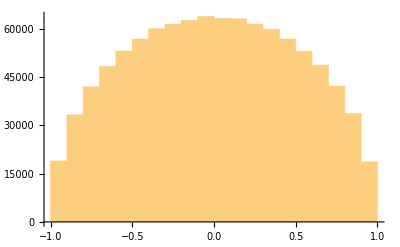
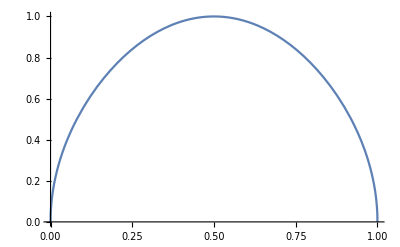

```mathematica
Overlay[{Histogram[xs],Plot[Sqrt[Sin[π x]],{x,0,1}]}]
```

```mathematica
Clear[x]
```

```mathematica
Integrate[Sqrt[Sin[π x]],{x,0,1}]
```

(2 √2 Gamma[3/4]^2)/π^(3/2)

```mathematica
Integrate[x Sqrt[Sin[π x]],{x,0,1}]/((2 √2 Gamma[3/4]^2)/π^(3/2))
```

(π Gamma[7/4])/(3 √2 Gamma[3/4]^2 Gamma[5/4])

```mathematica
N[%]
```

0.5

```mathematica
NIntegrate[x^2 Sqrt[Sin[π x]],{x,0,1}]/((2 √2 Gamma[3/4]^2)/π^(3/2))
```

0.310657

```mathematica
?Overlay
```

System`Overlay

Attributes[Overlay]={Protected,ReadProtected}
 
Options[Overlay]={Alignment→{Automatic,Automatic},Background→Automatic,BaselinePosition→Automatic,BaseStyle→{},ContentPadding→True,DefaultBaseStyle→Overlay,FrameMargins→Automatic,ImageMargins→0,ImageSize→Automatic}

```mathematica
Table[CatalanNumber[i],{i,1,10}]
```

{1,2,5,14,42,132,429,1430,4862,16796}

```mathematica
Expand[(1-q)^8]
```

1-8 q+28 q^2-56 q^3+70 q^4-56 q^5+28 q^6-8 q^7+q^8

```mathematica
126-84
```

42

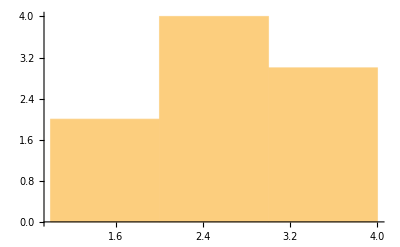

```mathematica
Histogram[{1,2,2,3,3,3,2,2,1}]
```

```mathematica
t=0;
For[i=0,i<100000, ++i,
{x,y,z,w}=Normalize[RandomVariate[NormalDistribution[0,1],4]];
t+=x*x];
t/100000
```

0.249594

```mathematica
t=0;
For[i=0,i<100000, ++i,
{x,y,z,w}=Normalize[RandomVariate[NormalDistribution[0,1],4]];
t+=x*x*x*x];
t/100000
```

0.125259

```mathematica
t=0;
For[i=0,i<1000000, ++i,
{x,y,z,w}=Normalize[RandomVariate[NormalDistribution[0,1],4]];
t+=x*x*x*x*x*x];
t/1000000
```

0.078295

```mathematica
Table[(Binomial[2n,n]-Binomial[2n,n-1])/2^(2n),{n,1,5}]//N
```

{0.25,0.125,0.078125,0.0546875,0.0410156}

```mathematica
Table[Binomial[2n,n]-Binomial[2n,n-1],{n,1,6}]
```

{1,2,5,14,42,132}

```mathematica
u=Quaternion[0,1,2,3]
```

Quaternion[0,1,2,3]

```mathematica
u^2
```

Quaternion[-14,0,0,0]

```mathematica
u=Quaternion[0,2,2,2]
```

Quaternion[0,2,2,2]

```mathematica
u*u
```

Quaternion[-12,0,0,0]

```mathematica
t=0;
n=10000;
For[i=0,i<n, ++i,
{x,y,z,w}=Normalize[RandomVariate[NormalDistribution[0,1],4]];
q=Quaternion[x,y,z,w];
r=Conjugate[q];
t+=(q-r)**(q-r)**(q-r)**(q-r)];
t/n
```

Quaternion[10.1015,7.40249×10^-19,-1.47319×10^-18,-3.45731×10^-18]

```mathematica
(q-r)**(q-r)
```

Quaternion[-3.37157,0.,0.,0.]

```mathematica
t=0;
n=10000;
For[i=0,i<n, ++i,
{x,y}=Normalize[RandomVariate[NormalDistribution[0,1],2]];
c=x+ⅈ y;
r=Conjugate[c];
t+=2
];
t/n
```

2

```mathematica
Clear[x]
```

```mathematica
Series[Sqrt[1-x],{x,0,10}]
```

1-x/2-x^2/8-x^3/16-(5 x^4)/128-(7 x^5)/256-(21 x^6)/1024-(33 x^7)/2048-(429 x^8)/32768-(715 x^9)/65536-(2431 x^10)/262144+O[x]^11

```mathematica
Table[Binomial[1/2,n](-1)^n,{n,0,10}]
```

{1,-1/2,-1/8,-1/16,-5/128,-7/256,-21/1024,-33/2048,-429/32768,-715/65536,-2431/262144}

```mathematica
Sum[Binomial[1/2,n]^2,{n,0,Infinity}]
```

4/π

```mathematica
t=0;
n=10000;
For[i=0,i<n, ++i,
{x,y}=Normalize[RandomVariate[NormalDistribution[0,1],2]];
c=x+ⅈ y;
r=Conjugate[c];
t+=Abs[1-c]
];
t/n
```

1.26473

```mathematica
Sqrt[1-Abs[c*r]]
```

0.

```mathematica
Abs[c*r]
```

1.

```mathematica
N[4/π]
```

1.27324

```mathematica
Clear[q,r]
```

```mathematica
((q-1)(1/r-1)-(1/q-1)(r-1))//Simplify
```

-((-1+q) (q-r) (-1+r))/(q r)

```mathematica
Clear[v,n,r]
```

```mathematica
v[r_,1]=2π r
```

2 π r

```mathematica
v[r_,n_]:=Integrate[v[r Sin[θ],n-1]r,{θ,0,π}];
Table[v[r,n],{n,1,6}]
```

{2 π r,4 π r^2,(8 π^2 r^3)/3,(64 π^2 r^4)/15,(64 π^3 r^5)/35,(2048 π^3 r^6)/945}

```mathematica
Table[v[r,n],{n,1,6}]
```

{2 π r,2 π^2 r^2,∫_0^π π^2 r^3 Csc[θ]ⅆθ,∫_0^π 3/4 π^3 r^4 Csc[θ]ⅆθ,∫_0^π 5/4 π^3 r^5 Csc[θ]ⅆθ,∫_0^π 35/64 π^4 r^6 Csc[θ]ⅆθ}

```mathematica
s[n_]:=(2 π^((n+1)/2)r^n)/Gamma[(n+1)/2]
```

```mathematica
Table[s[n],{n,1,6}]
```

{2 π r,4 π r^2,2 π^2 r^3,(8 π^2 r^4)/3,π^3 r^5,(16 π^3 r^6)/15}

```mathematica
945/11
```

945/11

```mathematica
v[r_,1]=2r;
v[r_,n_]:=Integrate[v[r Sin[θ],n-1]r Sin[θ],{θ,0,π}];
Table[v[r,n],{n,1,6}]
```

{2 r,π r^2,(3 π r^3)/2,(5 π^2 r^4)/8,(35 π^2 r^5)/48,(63 π^3 r^6)/256}

```mathematica
Integrate[2 r Sin[θ]r Sin[θ],{θ,0,π}]
```

π r^2

```mathematica
Integrate[π(r Sin[θ])^2 r Sin[θ],{θ,0,π}]
```

(4 π r^3)/3

```mathematica
Integrate[(4 π (r Sin[θ])^3)/3 r Sin[θ],{θ,0,π}]
```

(π^2 r^4)/2

```mathematica
ClearAll[v]
```

```mathematica
v[r_,1]=2r;
v[r_,n_]=Integrate[v[r Sin[θ],n-1]r Sin[θ],{θ,0,π}];
Table[v[r,n],{n,1,6}]
```

{2 r,π r^2,(3 π r^3)/2,(5 π^2 r^4)/8,(35 π^2 r^5)/48,(63 π^3 r^6)/256}

```mathematica
v[r,2]
```

π r^2

```mathematica
Integrate[v[r Sin[θ],2]r Sin[θ],{θ,0,π}]
```

(3 π r^3)/2

```mathematica
Integrate[π(r Sin[θ])^2 r Sin[θ],{θ,0,π}]
```

(4 π r^3)/3

```mathematica
v[r Sin[θ],2]r Sin[θ]
```

3/4 π r^3 Sin[θ]

```mathematica
v[r Sin[θ],2]
```

(3 π r^2)/4

```mathematica
v[x,2]/.x->r Sin[θ]
```

π r^2 Sin[θ]^2

```mathematica
v[r,2]
```

π r^2

```mathematica
v[r Sin[θ],2]
```

(3 π r^2)/4

```mathematica
v[r_,1]:=2r;
v[r_,n_]:=Block[{θ},Integrate[v[r Sin[θ],n-1]r Sin[θ],{θ,0,π}]];
Table[v[r,n],{n,1,6}]
```

{2 r,π r^2,(3 π r^3)/2,(5 π^2 r^4)/8,(35 π^2 r^5)/48,(63 π^3 r^6)/256}

```mathematica
Module[θ,∫_0^π v[r Sin[θ],2-1] r Sin[θ]ⅆθ]
```

Module[θ,∫_0^π v[r Sin[θ],2-1] r Sin[θ]ⅆθ]

```mathematica
∫_0^π v[r Sin[θ],2-1] r Sin[θ]ⅆθ
```

π r^2

```mathematica
v[r_,1]:=2r;
v[r_,n_]:=Integrate[v[r Sin[θ],n-1]r Sin[θ],{θ,0,π}];
Table[v[r,n],{n,1,6}]
```

{2 r,π r^2,(3 π r^3)/2,(5 π^2 r^4)/8,(35 π^2 r^5)/48,(63 π^3 r^6)/256}

```mathematica
v[r_,1]:=2r;
v[r_,n_]:=Block[{θ},Integrate[v[r Sin[θ],n-1]r Sin[θ],{θ,0,π}]];
Table[v[r,n],{n,1,6}]
```

{2 r,π r^2,(3 π r^3)/2,(5 π^2 r^4)/8,(35 π^2 r^5)/48,(63 π^3 r^6)/256}

```mathematica
v[r_,1]:=2r;
v[r_,n_]:=Module[{θ},Integrate[v[r Sin[θ],n-1]r Sin[θ],{θ,0,π}]];
Table[v[r,n],{n,1,6}]
```

{2 r,π r^2,(4 π r^3)/3,(π^2 r^4)/2,(8 π^2 r^5)/15,(π^3 r^6)/6}